```mathematica
MyList[n_,p_]:=ReadList[StringJoin["d:\\Triangle\\Data\\",ToString[n],"_",ToString[p],".txt"],Number]
```

```mathematica
ShortList[n_,p_] := Select[ MyList[n,p], # < 10^10&]
```

```mathematica
lengthData=Table[{p,Length[ShortList[3,p]]},{p,{3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59}}]
```

{{3,15},{5,105},{7,508},{11,2178},{13,3810},{17,10693},{19,10619},{23,11731},{29,26553},{31,39268},{37,80012},{41,108352},{43,117466},{47,262336},{53,445697},{59,121194}}

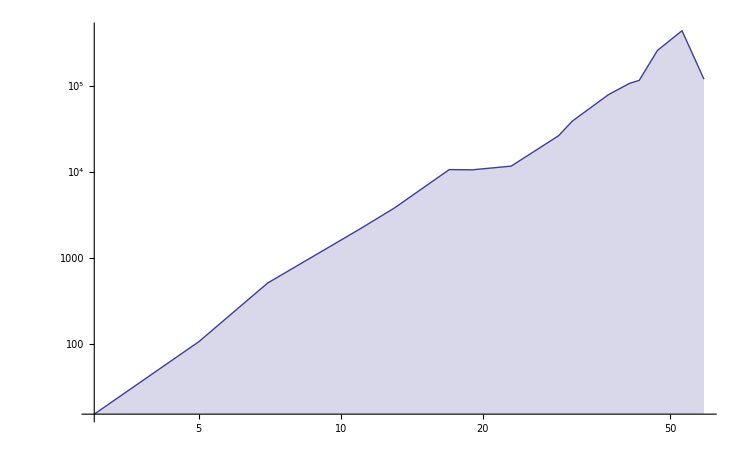

```mathematica
ListLogLogPlot[lengthData, Joined->True, Filling->Axis]
```

```mathematica
Table[Prime[i], {i,2,50}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229}